```mathematica
f[x_]:=a*E^(-(x-b)^2/(2*c^2))
```

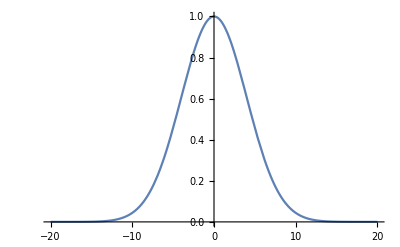

```mathematica
a=1;
b=0;
c=4;
Plot[f[x],{x,-20,20},PlotRange->Full]
```

```mathematica
TraditionalForm[f[x]]
```

ⅇ^(-x^2/32)

```mathematica
probs=N@f[Range[-15,15]]
```

{0.000883826,0.00218749,0.00508607,0.011109,0.0227942,0.0439369,0.0795595,0.135335,0.216265,0.324652,0.457833,0.606531,0.75484,0.882497,0.969233,1.,0.969233,0.882497,0.75484,0.606531,0.457833,0.324652,0.216265,0.135335,0.0795595,0.0439369,0.0227942,0.011109,0.00508607,0.00218749,0.000883826}

```mathematica
probsNorm={probs*(1/Total[probs])}
```

{{0.0000881579,0.000218193,0.000507314,0.00110808,0.00227362,0.00438252,0.00793572,0.0134991,0.0215715,0.0323827,0.0456669,0.0604989,0.0752921,0.0880253,0.0966769,0.0997458,0.0966769,0.0880253,0.0752921,0.0604989,0.0456669,0.0323827,0.0215715,0.0134991,0.00793572,0.00438252,0.00227362,0.00110808,0.000507314,0.000218193,0.0000881579}}

```mathematica
probNormGraph=Transpose@Join[{Range[-15,15]},probsNorm]
```

{{-15,0.0000881579},{-14,0.000218193},{-13,0.000507314},{-12,0.00110808},{-11,0.00227362},{-10,0.00438252},{-9,0.00793572},{-8,0.0134991},{-7,0.0215715},{-6,0.0323827},{-5,0.0456669},{-4,0.0604989},{-3,0.0752921},{-2,0.0880253},{-1,0.0966769},{0,0.0997458},{1,0.0966769},{2,0.0880253},{3,0.0752921},{4,0.0604989},{5,0.0456669},{6,0.0323827},{7,0.0215715},{8,0.0134991},{9,0.00793572},{10,0.00438252},{11,0.00227362},{12,0.00110808},{13,0.000507314},{14,0.000218193},{15,0.0000881579}}

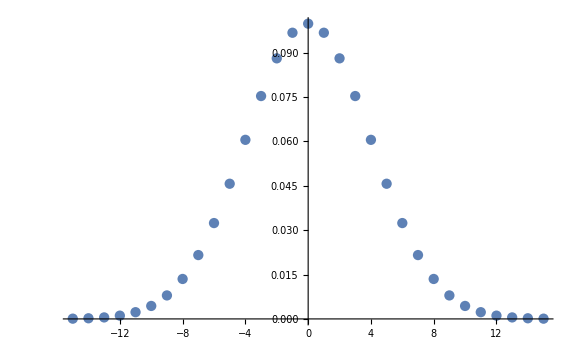

```mathematica
ListPlot[probNormGraph,ImageSize->Large]
```